```mathematica
(*3D Plot*)
```

```mathematica
folder = NotebookDirectory[] <> "PlotData/";
SetDirectory[folder];
sets =Sort[ToExpression[FileNames[]]];
Manipulate[
label = "Densidad, " <> ToString[sets[[set]]] <> " partículas";
filePath = folder <>ToString[sets[[set]]] <>"/dump_densidad.csv";
Data = Import[filePath];
ListPlot3D[Data, AxesLabel->{Style["x",14], Style["y",14], Style["ρ",14]}, PlotLabel->Style[label,14],PlotRange->All,ImageSize->Medium]
ListDensityPlot[Data, PlotRange->Automatic, Mesh->38, PlotLabel->Style[label,14],ImageSize->Medium]
,{set,1,Length[sets],1}]
```

```mathematica
(*2D Plot*)
```

```mathematica
folder = NotebookDirectory[] <> "PlotData/";
SetDirectory[folder];
sets =Sort[ToExpression[FileNames[]]];
Manipulate[
labelD = "Densidad (Sección transversal), " <> ToString[sets[[set]]] <> " partículas";
filePathD =  folder <>ToString[sets[[set]]] <>"/flatGrid.csv";
DataFlat = Import[filePathD];
Show[ListPlot[{DataFlat}, AxesOrigin->{0,0}, PlotRange->All, PlotStyle->PointSize[Large], GridLines->Automatic, AxesLabel->{Style["x",14], Style["ρ",14]}, PlotLabel->Style[labelD,14],AspectRatio->1]]
,{set,1,Length[sets],1}]
```

```mathematica
(*Densidad vs número de partículas, tamaño caja 20 sigmas*)
```

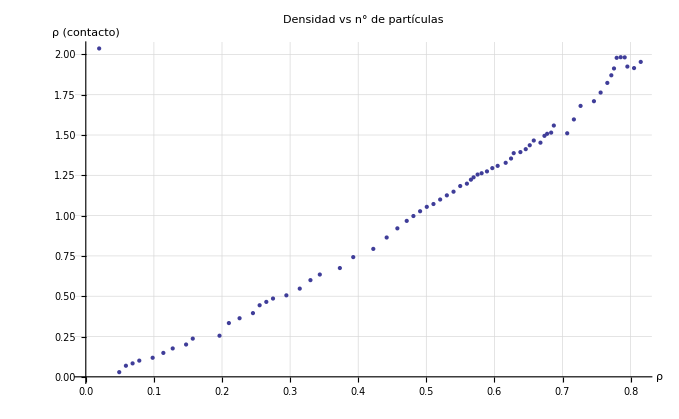

```mathematica
folder = NotebookDirectory[] <> "PlotData/";
SetDirectory[folder];
sets =Sort[ToExpression[FileNames[]]];
NPoints = 11;
EvalPoint = 1;
For[i=1; dataList = {}, i<Length[sets], i++,AppendTo[dataList, sets[[i]]]]

For[i=1; cValues={},i<=Length[dataList],i++,
dir = folder <>ToString[sets[[i]]] <> "/flatGrid.csv";
DataFlat = Import[dir];
For[j=2; fewData={}, j<NPoints, j++, AppendTo[fewData, DataFlat[[j]]]];
AppendTo[cValues,{(π/4)*(dataList[[i]])/20^2,asimov[EvalPoint]}];
asimov[x_]=Fit[fewData,{1,x,x^2,x^3},x];
]
ListPlot[cValues,PlotStyle->PointSize[Medium],GridLines->Automatic,AxesLabel->{Style["ρ",14],Style["ρ (contacto)",14]},PlotLabel->Style["Densidad vs n° de partículas",14],AxesOrigin->{0,0}]
```